# Coulb 1 Behavior Analysis Tests

## SPP026 141014 (now with unambiguous codes as well as TTL 0 reset fix)

## Initial

```mathematica
<<PyonpyonW`
```

HokahokaW`
(origin)[https://ktakagaki@github.com/ktakagaki/HokahokaW.git]
current Git HEAD:  24161a64fcfb50b8fa0954799b3d1b8272601b67
newest file:  Thu 16 Oct 2014 19:12:26

NounouW`
(origin)[https://ktakagaki@github.com/ktakagaki/NounouW.git]
current Git HEAD:  a9640024c05037332c61a2a21ebd1a15d04fda22
newest file:  Thu 16 Oct 2014 19:12:07

<<Set JLink` java stack size to 6144Mb>>

ParaparaW`
(origin)[https://ktakagaki@bitbucket.org/ktakagaki/paraparaw.git]
current Git HEAD:  4406a93fa653ba2c56f76a227d593c027bdb3d0b
newest file:  Thu 16 Oct 2014 19:12:26

PyonpyonW`
(origin)[https://ktakagaki@bitbucket.org/ktakagaki/pyonpyonw.git]
current Git HEAD:  750f1bc327c59d96f0fa2237cf3d79da53658b60
newest file:  Thu 16 Oct 2014 20:05:01

```mathematica
coulb1Folder="U:\\VSDdata\\project.SPP\\SPP.Coulb1"(*\_arch"*);
nlx2Folder="U:\\VSDdata\\project.SPP\\SPP.Nlx2"(*\_arch"*);
subjectString="SPP026";
date={2014,10, 15};
```

```mathematica
{videoFile}=FileNames[FileNameJoin[{coulb1Folder,subjectString,
	ToString[date[[1]]]<>"-"<>ToString[date[[2]]]<>"-"<>ToString[date[[3]]]<>" *.wmv"}]]
```

{U:\VSDdata\project.SPP\SPP.Coulb1\SPP026\2014-10-15 15-29-07.056.wmv}

```mathematica
{nlxNevFile}=FileNames[FileNameJoin[{nlx2Folder,subjectString,ToString[date[[1]]]<>"-"<>ToString[date[[2]]]<>"-"<>ToString[date[[3]]]<>"*", "Events.nev"}]]
```

{U:\VSDdata\project.SPP\SPP.Nlx2\SPP026\2014-10-15_15-20-03\Events.nev}

## Import Events

```mathematica
{eventObj}=NNDataReader`load[nlxNevFile]
```

{«JavaObject[nounou.data.XEvents]»}

```mathematica
events=NNToList[eventObj];
```

### Ouptut For Troubleshooting

```mathematica
SortBy[events, #[[2]]&]//TableForm
```

0 | -9223372028717672637 | 0 | 0 | Starting Recording
100000001 | -9223372028673889637 | 0 | 0 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0000).
100000001 | -9223372028673877605 | 14796937 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000001 | -9223372028659068168 | 173522344 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
100000000 | -9223372028485554199 | 249500 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372028485535574 | 4000812 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372028481524887 | 638125 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372028480871574 | 9687 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372028480851637 | 15749532 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372028465110699 | 249812 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372028465092355 | 1630312 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372028463456324 | 10156 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
100000001 | -9223372028463435918 | 9700781 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000001 | -9223372028453725855 | 14009531 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
100000000 | -9223372028439724668 | 250688 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372028439706293 | 4001125 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372028435695324 | 666250 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372028435019418 | 10313 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372028434999199 | 20158937 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372028414848387 | 250094 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372028414830387 | 4001000 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372028410819480 | 10156 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372028410791512 | 5587563 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000001 | -9223372028405194293 | 0 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
100000000 | -9223372028387722074 | 251281 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372028387713574 | 31 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
100000001 | -9223372028387703574 | 4001344 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372028383692324 | 9875 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372028383670137 | 25777063 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372028357902074 | 249781 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372028357883605 | 2818437 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372028355055480 | 1013187 | 24 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0018).
100000001 | -9223372028354032512 | 10094 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372028354012355 | 17823812 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372028336197262 | 249188 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372028336178824 | 4001312 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372028332167480 | 710906 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372028331446668 | 10063 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372028331426387 | 16226344 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372028315215387 | 249813 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372028315192043 | 4001219 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372028311180699 | 1280906 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372028309889918 | 14000 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372028309869730 | 16143593 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372028293734230 | 247406 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372028293716168 | 4001125 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372028289705074 | 10281 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372028289684574 | 19886656 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372028269810480 | 249500 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372028269788480 | 4000218 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372028265778355 | 661406 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372028265107199 | 10031 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372028265087168 | 24536938 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372028240558730 | 250093 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372028240530105 | 4011500 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372028236511293 | 9188 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372028236491949 | 8370187 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000001 | -9223372028228111855 | 11993468 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
100000000 | -9223372028216126762 | 249219 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372028216108418 | 1595063 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372028214503105 | 863687 | 24 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0018).
100000001 | -9223372028213629418 | 9969 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372028213592199 | 25699844 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372028187901012 | 248907 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372028187882512 | 4001125 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372028183870918 | 1068125 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372028182793230 | 10062 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372028182773168 | 16106750 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372028166678137 | 249813 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372028166658824 | 4000219 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372028162648730 | 10125 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372028162628543 | 18855750 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372028143781574 | 255750 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372028143763012 | 4001250 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372028139751793 | 14219 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372028139731605 | 19212593 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372028120527605 | 249781 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372028120509230 | 4001218 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372028116498074 | 10219 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372028116477793 | 21091719 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372028095394230 | 249781 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372028095376293 | 4000219 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372028091366074 | 757656 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372028090599199 | 10094 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372028090578637 | 19569094 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372028071023762 | 249782 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372028071000199 | 4001094 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372028066989043 | 9781 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372028066968949 | 3985906 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000001 | -9223372028062973074 | 18652062 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
100000000 | -9223372028044337918 | 244719 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372028044311480 | 4000187 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372028040301387 | 572125 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372028039720387 | 10157 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372028039700199 | 18875719 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372028020832824 | 244719 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372028020814637 | 4001188 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372028016803293 | 9969 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372028016783199 | 21270719 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027995521137 | 251282 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372027995502699 | 4001281 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372027991491668 | 11906 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372027991470043 | 17157188 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027974321262 | 256657 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372027974303043 | 4000344 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372027970292918 | 430219 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372027969852762 | 9907 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372027969832762 | 20672969 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027949168449 | 249781 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372027949148074 | 4001437 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372027945138043 | 10344 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372027945117762 | 24605938 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027920520480 | 249781 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372027920501605 | 3999781 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372027916492012 | 1160094 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372027915322949 | 10062 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372027915302730 | 19635812 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027895677637 | 248032 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372027895657230 | 4001343 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372027891646043 | 10063 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372027891625887 | 21643875 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027869990637 | 254563 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372027869972355 | 4000625 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372027865962230 | 434218 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372027865518043 | 9938 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372027865498043 | 19670750 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027845835762 | 250688 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372027845817418 | 4001125 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372027841804199 | 10031 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372027841783637 | 25200469 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027816591449 | 248875 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372027816573449 | 1223094 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372027815339824 | 9469 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
100000001 | -9223372027815320168 | 26000875 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027789327824 | 251312 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372027789309199 | 4000937 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372027785298293 | 10156 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372027785278137 | 22772000 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027762515043 | 250375 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372027762496418 | 4000125 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372027758486449 | 1148094 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372027757329387 | 10094 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372027757307793 | 23784594 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027733532918 | 247688 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372027733513418 | 4001156 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372027729502199 | 1726156 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372027727766293 | 10000 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372027727746012 | 19833688 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027707921449 | 251562 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372027707902543 | 4001313 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372027703891512 | 10282 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372027703864512 | 22348063 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027681525262 | 245907 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372027681506668 | 4001594 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372027677495574 | 10062 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372027677471012 | 21757750 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027655721824 | 250687 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372027655703730 | 4001156 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372027651692668 | 2445625 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372027649237512 | 10032 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372027649217387 | 23279313 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027625950168 | 249781 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372027625930699 | 4001250 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372027621919387 | 5999094 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372027615910105 | 16638843 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027599282855 | 249812 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372027599261637 | 4001063 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372027595250637 | 581532 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372027594655074 | 7531 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372027594637293 | 7378031 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000001 | -9223372027587256043 | 12152250 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
100000000 | -9223372027575112449 | 264719 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372027575093949 | 4001281 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372027571082824 | 12375 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372027571059512 | 18010594 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027553057668 | 250406 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372027553039043 | 4000250 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372027549028762 | 390250 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372027548628855 | 9937 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372027548606855 | 17978843 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027530637387 | 249500 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372027530618137 | 4001000 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372027526605293 | 542344 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372027526053105 | 10125 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372027526032980 | 23046031 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027503015699 | 249781 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372027502977324 | 4000219 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372027498967230 | 10125 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372027498944980 | 18323593 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027480629762 | 250094 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372027480610480 | 4005500 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372027476595387 | 1018344 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372027475567199 | 9875 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372027475547105 | 16767562 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027458788480 | 250375 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372027458769605 | 4001031 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372027454758543 | 9969 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372027454735480 | 17574000 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027437170293 | 250094 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372027437151949 | 4001156 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372027433134762 | 430000 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372027432694855 | 12000 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372027432673387 | 22014657 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027410668387 | 247688 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372027410649105 | 4001312 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372027406637980 | 579750 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372027406048980 | 10187 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372027406028637 | 18035282 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027388012824 | 249812 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372027387984074 | 4001000 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372027383972980 | 468062 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372027383495168 | 10156 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372027383474793 | 16868563 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027366615262 | 250094 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372027366592980 | 3999687 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372027362583355 | 10062 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372027362563105 | 9336250 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000001 | -9223372027353217105 | 11514687 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
100000000 | -9223372027341711793 | 249813 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372027341692668 | 4000344 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372027337682543 | 409469 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372027337263449 | 10000 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372027337243324 | 24382469 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027312870605 | 248312 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372027312851105 | 4001312 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372027308840512 | 430063 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372027308401418 | 10063 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372027308381199 | 19670625 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027288719324 | 249812 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372027288700762 | 4001282 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372027284689668 | 10094 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372027284667637 | 328438 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000001 | -9223372027284329543 | 10462375 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
100000001 | -9223372027273856918 | 6052219 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
100000001 | -9223372027267794980 | 2005000 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
100000000 | -9223372027265815293 | 250094 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372027265785793 | 4001250 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372027261774605 | 9875 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372027261754605 | 124968 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000001 | -9223372027261619699 | 16183531 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
100000001 | -9223372027245426168 | 373188 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
100000000 | -9223372027245063043 | 242313 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372027245043230 | 4001218 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372027241032137 | 328219 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372027240694043 | 9969 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372027240667199 | 23167281 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027217508855 | 250093 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372027217490230 | 4001250 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372027213479199 | 22531 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372027213451574 | 20338406 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027193121668 | 251000 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372027193103293 | 4001125 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372027189092324 | 382281 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372027188700230 | 10031 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372027188680105 | 20657906 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027168030980 | 249812 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372027168012387 | 3223219 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372027164779355 | 1167187 | 24 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0018).
100000001 | -9223372027163602355 | 10156 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372027163582168 | 24113969 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027139483324 | 250094 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372027139458480 | 4001187 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372027135447387 | 10063 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372027135427074 | 21168781 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027114267199 | 249500 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372027114248605 | 4001281 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372027110237480 | 509093 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372027109719480 | 10125 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372027109699199 | 21410812 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027088297699 | 257562 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372027088278324 | 4001094 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372027084266168 | 423719 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372027083832574 | 10219 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372027083811230 | 17233593 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027066586293 | 253063 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372027066567730 | 4001062 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372027062556855 | 10156 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372027062533762 | 24536157 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027038009105 | 248625 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372027037987887 | 4001313 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372027033976605 | 9875 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372027033956637 | 19043750 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372027014921449 | 249781 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372027014902949 | 4001094 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372027010891887 | 10750 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372027010870480 | 1957906 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000001 | -9223372027008902699 | 21946719 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
100000000 | -9223372026986964449 | 249812 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372026986946137 | 4001375 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372026982934730 | 421000 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372026982503918 | 10000 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372026982483699 | 16336531 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026966155730 | 249500 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372026966134418 | 3999406 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372026962125230 | 10093 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372026962105012 | 18077750 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026944035855 | 250093 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372026944017387 | 4002844 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372026940001574 | 7375 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372026939984262 | 17996719 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026922010949 | 242937 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372026921974699 | 4001125 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372026917963324 | 406750 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372026917546699 | 10219 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372026917525855 | 25430312 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026892104012 | 249782 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372026892085762 | 4009094 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372026888071324 | 426812 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372026887634637 | 10157 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372026887613855 | 22879750 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026864745105 | 249781 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372026864724449 | 4001062 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372026860713637 | 10094 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372026860693355 | 22454843 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026838247074 | 255750 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372026838228699 | 4000375 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372026834218512 | 981000 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372026833227668 | 10125 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372026833197637 | 16159750 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026817048730 | 253375 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372026817028043 | 4001219 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372026813017012 | 10344 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372026812996762 | 17807125 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026795198480 | 244406 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372026795180262 | 4001188 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372026791169074 | 10187 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372026791149012 | 17285094 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026773873480 | 248281 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372026773854480 | 4001187 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372026769843262 | 846563 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372026768989449 | 10125 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372026768969105 | 22989812 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026745987855 | 253093 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372026745968512 | 4001219 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372026741958449 | 566437 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372026741382355 | 10062 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372026741362230 | 16067687 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026725303074 | 249812 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372026725284012 | 4000469 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372026721256824 | 6344 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372026721239980 | 21618312 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026699630980 | 249218 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372026699611168 | 4002344 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372026695597980 | 466687 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372026695121668 | 9969 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372026695101480 | 23048250 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026672062449 | 250094 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372026672043824 | 4001094 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372026668032887 | 10157 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372026668012543 | 19523625 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026648497918 | 250406 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372026648477762 | 4002094 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372026644466012 | 10094 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372026644445637 | 5540282 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000001 | -9223372026638895730 | 14208781 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
100000000 | -9223372026624695387 | 249500 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372026624678293 | 4001313 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372026620649699 | 398687 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372026620241137 | 10250 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372026620220918 | 19689563 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026600548887 | 248000 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372026600522418 | 4001188 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372026596511168 | 10000 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372026596491105 | 13450437 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000001 | -9223372026583030824 | 7641469 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
100000000 | -9223372026575398168 | 248594 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372026575379387 | 4000188 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372026571369355 | 1573093 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372026569786387 | 10219 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372026569765355 | 14785156 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026554989605 | 262343 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372026554970699 | 4000125 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372026550960730 | 10093 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372026550940387 | 21878188 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026529073262 | 245313 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372026529052762 | 4001094 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372026525041793 | 10219 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372026525021605 | 25343937 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026499686199 | 249781 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372026499658449 | 4001219 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372026495647793 | 810281 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372026494827730 | 10156 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372026494801512 | 23768969 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026471041199 | 249781 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372026471022387 | 3999782 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372026467001949 | 2437 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372026466991543 | 1280219 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000001 | -9223372026465701512 | 20389875 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
100000000 | -9223372026445321043 | 250094 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372026445301949 | 4001406 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372026441290699 | 811031 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372026440466355 | 9843 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372026440446480 | 40843 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000001 | -9223372026440397137 | 53875 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
100000001 | -9223372026440331605 | 16526562 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
100000000 | -9223372026423813887 | 250375 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372026423792793 | 4000031 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372026419783043 | 394188 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372026419378949 | 10125 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372026419358887 | 18140813 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026401226418 | 249469 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372026401205262 | 3997250 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372026397196699 | 8562 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372026397178012 | 16425594 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026380761137 | 249500 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372026380742230 | 4005625 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372026376727543 | 486219 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372026376231512 | 10063 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372026376210949 | 19491375 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026356728074 | 249781 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372026356709824 | 4001656 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372026352698480 | 9875 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372026352678543 | 22638063 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026330049105 | 255781 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372026330030730 | 4000500 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372026326020762 | 441157 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372026325569668 | 10031 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372026325549543 | 24380906 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026301177137 | 259938 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372026301158855 | 4001218 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372026297147637 | 17282 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372026297118543 | 22680969 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026274446199 | 253687 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372026274427730 | 4001062 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372026270416730 | 374093 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372026270032574 | 10000 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372026270012574 | 22222844 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026247798262 | 249782 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372026247779949 | 4001375 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372026243768855 | 10093 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372026243748355 | 24310625 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026219445887 | 253375 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372026219427918 | 4001281 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372026215416762 | 470938 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372026214936512 | 9875 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372026214916043 | 24685313 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026190239199 | 248875 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372026190220887 | 4000219 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372026186206980 | 6500 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372026186190637 | 20682813 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026165516105 | 250687 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372026165497824 | 4001031 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372026161486668 | 399000 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372026161076543 | 9719 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372026161056699 | 18931687 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026142146574 | 249781 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372026142124574 | 4000562 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372026138113980 | 10156 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372026138093730 | 17130468 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026120972387 | 249813 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372026120953449 | 4000219 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372026116943199 | 443156 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372026116490262 | 10125 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372026116459637 | 21901375 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026094566605 | 250968 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372026094548512 | 4001219 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372026090537355 | 13375 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372026090514230 | 16733718 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026073788668 | 252188 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372026073770699 | 4001375 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372026069758793 | 643250 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372026069105637 | 10125 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372026069082605 | 22644031 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026046447074 | 251000 | 1 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).
100000001 | -9223372026046428793 | 4001156 | 64 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0040).
100000001 | -9223372026042417480 | 558250 | 16 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0010).
100000001 | -9223372026041850699 | 10094 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
100000001 | -9223372026041830512 | 18388844 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000000 | -9223372026023450168 | 249469 | 2 | TTL Input on AcqSystem1_0 board 0 port 0 value (0x0002).
100000001 | -9223372026023432012 | 4001500 | 128 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0080).
100000001 | -9223372026019420730 | 10187 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
100000001 | -9223372026019398074 | 525814687 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
100000001 | -9223372025474906637 | 0 | 199 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x00C7).
100000001 | -9223372025474906605 | 0 | 255 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x00FF).
0 | -9223372025442739637 | 0 | 0 | Stopping Recording

```mathematica
(*SetDirectory[NotebookDirectory[]];Export["Test_Coulb1_Analysis_SPP026.141010.tsv", ReplacePart[#,2->#[[2]]+9223372033667928359]&/@events]*)
```

### Sorting

```mathematica
eventPorts=eventObj@ports[]
```

{0,100000000,100000001}

```mathematica
events0=Select[events,(#[[1]]==eventPorts[[1]])&];
events1=Select[events,(#[[1]]==eventPorts[[2]])&];
events2=Select[events,(#[[1]]==eventPorts[[3]])&];

events0= ReplacePart[#, 1->"Neuralynx"]& /@ events0;
events1= ReplacePart[#, 1->"Stimulus"]& /@ events1;
events2= ReplacePart[#, 1->"Colbourn"]& /@ events2;

Print["Neuralynx events: "<> ToString[Length[events0]]];
Print[events0//TableForm];
Print["Stimulus events: "<> ToString[Length[events1]]];
Print["Colbourne events: "<> ToString[Length[events2]]];
```

Neuralynx events: 2

Neuralynx | -9223372026025197299 | 0 | 0 | Starting Recording
Neuralynx | -9223372023197398299 | 0 | 0 | Stopping Recording

Stimulus events: 100

Colbourne events: 488

## Filter Out False Port Changes: Colbourn Bit Transition Bug (set new bits-then-unset old bits)

```mathematica
Dimensions[events2]
```

{488,5}

### Notes on the problem

Look at this crap ...
The Colbourn system always sets the new on bits (within one cycle, always, it seems), and then stepwise, goes through the new off bits, unsetting them one by one

-Graphics-

### Normalize Timing for Easier Display

```mathematica
(*events0=ReplacePart[#,2->#[[2]]+9223372033667928359]&/@events0;
events1=ReplacePart[#,2->#[[2]]+9223372033667928359]&/@events1;
events2=ReplacePart[#,2->#[[2]]+9223372033667928359]&/@events2;*)
```

### Correct Bit Transition Bug

```mathematica
events2=PPCorrectColbournRecordedEvents[events2, 3];
```

The following timestamps were removed: {}

```mathematica
events2=PPCorrectColbournRecordedEvents[events2, 2];
```

The following timestamps were removed: {}

```mathematica
events2=PPCorrectColbournRecordedEvents[events2, 1];
```

The following timestamps were removed: {-9223372025734012861, -9223372025712498017, -9223372024891123986, -9223372024869693392, -9223372024562741330, -9223372024209891049, -9223372024180921830, -9223372024154626986, -9223372024131666424, -9223372024057486674, -9223372024012602080, -9223372023879672580, -9223372023559108142, -9223372023461870236}

### Correct Other Flow Irregularities

```mathematica
events2=PPCorrectColbournFlow[events2];
```

### Summary

```mathematica
Dimensions[events2]
```

{474,5}

```mathematica
events2//TableForm
```

Colbourn | -9223372025973341174 | 32 | 32 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0020).
Colbourn | -9223372025973340111 | 48180844 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025925157799 | 46142125 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
Colbourn | -9223372025879015267 | 58455531 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
Colbourn | -9223372025820558830 | 29092063 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
Colbourn | -9223372025791466455 | 4000969 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372025787464705 | 2542281 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372025784921580 | 1094 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372025784919049 | 17052407 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025767866049 | 4001375 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372025763863955 | 402375 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372025763460955 | 0 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372025763459830 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372025763458549 | 25065938 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025738391924 | 4001219 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372025734389767 | 376468 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372025734012892 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Colbourn | -9223372025734012361 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372025734010424 | 17509532 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025716499986 | 4001062 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372025712498049 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025712497049 | 32 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372025712495892 | 22500968 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025689994330 | 763625 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372025689230267 | 1237343 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372025687992236 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Colbourn | -9223372025687992205 | 1063 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372025687990080 | 18691938 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025669297611 | 4001375 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372025665295424 | 341219 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372025664953455 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Colbourn | -9223372025664953424 | 1157 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372025664951236 | 8367406 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025656583111 | 17002875 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
Colbourn | -9223372025639579486 | 2513312 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372025637065549 | 532 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Colbourn | -9223372025637064017 | 25323218 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025611737580 | 3998375 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372025607738455 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025607738424 | 1125 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372025607736174 | 8181313 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025599554174 | 15954813 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
Colbourn | -9223372025583598580 | 4000375 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372025579597424 | 762344 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372025578834361 | 0 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372025578833361 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372025578831986 | 20641656 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025558189705 | 4001313 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372025554187549 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025554187517 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372025554186299 | 32 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372025554185080 | 21919594 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025532264705 | 4000438 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372025528263642 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372025528262549 | 32 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372025528261517 | 18934062 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025509326986 | 4000437 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372025505325861 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372025505324767 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372025505323517 | 1452062 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025503870736 | 14415812 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
Colbourn | -9223372025489454049 | 9640344 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
Colbourn | -9223372025479812861 | 4000344 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372025475811705 | 453094 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372025475357736 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Colbourn | -9223372025475357705 | 1156 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372025475355299 | 19261438 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025456093080 | 4001250 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372025452090892 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372025452089736 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372025452088674 | 22573907 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025429514174 | 4000282 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372025425512955 | 416250 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372025425096049 | 1282 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372025425093892 | 18074968 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025407018392 | 4047437 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
Colbourn | -9223372025402970174 | 4001282 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372025398968142 | 475375 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372025398492017 | 1156 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372025398489799 | 19184657 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025379304330 | 4001250 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372025375302017 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025375301986 | 906 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372025375299861 | 25847062 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025349452205 | 879031 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372025348572174 | 915219 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372025347656267 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Colbourn | -9223372025347656236 | 0 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372025347655205 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372025347654142 | 22574250 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025325079236 | 4003000 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372025321075830 | 3669031 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372025317406392 | 2531 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372025317403236 | 9116812 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025308285674 | 10916407 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
Colbourn | -9223372025297368486 | 4001312 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372025293366361 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025293366330 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372025293365111 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372025293364205 | 19818063 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025273543705 | 4000406 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372025269542330 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025269542299 | 875 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372025269540267 | 7092906 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025262446736 | 9909031 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
Colbourn | -9223372025252536861 | 4000312 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372025248535611 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025248535580 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372025248534017 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372025248533111 | 1339594 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025247192549 | 20375782 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
Colbourn | -9223372025226816017 | 4001406 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372025222813642 | 0 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372025222412174 | 32 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
Colbourn | -9223372025222411799 | 0 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372025222410642 | 31 | 12 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000C).
Colbourn | -9223372025222409455 | 16403781 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025206005299 | 4002032 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372025202002767 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372025202002017 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372025202001517 | 16721281 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025185279517 | 4000750 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372025181278361 | 492250 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372025180785424 | 1313 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372025180782955 | 22517656 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025158264642 | 1751343 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
Colbourn | -9223372025156512361 | 4001156 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372025152510330 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025152510299 | 969 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372025152508174 | 3823219 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025148684517 | 13255000 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
Colbourn | -9223372025135428830 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372025131427424 | 32 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372025131426580 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025131426549 | 1094 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372025131424486 | 18506812 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025112917017 | 4000437 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372025108915861 | 377406 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372025108538017 | 718 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372025108536174 | 22917500 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025085617924 | 1151063 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372025084466486 | 894656 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372025083570861 | 0 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372025083569892 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372025083568642 | 14851593 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025068716455 | 5136500 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
Colbourn | -9223372025063579299 | 4001438 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372025059577080 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025059577049 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372025059575955 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372025059574986 | 17546969 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025042027455 | 2297563 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372025039729424 | 2695469 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372025037033111 | 1000 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372025037031111 | 15120719 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372025021909830 | 3316406 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
Colbourn | -9223372025018592611 | 4001250 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372025014590455 | 865688 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372025013724455 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Colbourn | -9223372025013724424 | 0 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372025013723361 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372025013722361 | 23291062 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024990430705 | 4000469 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372024986429611 | 595344 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372024985833267 | 843 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372024985831299 | 12066563 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024973763767 | 7367218 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
Colbourn | -9223372024966394924 | 4000719 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372024962393705 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024962393674 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372024962392517 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372024962391517 | 17703687 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024944687017 | 4001531 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372024940684705 | 626750 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372024940057080 | 0 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372024940056517 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372024940055861 | 21478094 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024918577174 | 4001313 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372024914574892 | 527125 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372024914047049 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Colbourn | -9223372024914047017 | 0 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372024914045955 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372024914044892 | 18456812 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024895587267 | 4001406 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372024891585236 | 460281 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372024891124017 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Colbourn | -9223372024891123080 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372024891121986 | 17425719 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024873695580 | 4001313 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372024869693424 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024869692392 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372024869691017 | 20129750 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024849560736 | 3191344 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372024846368424 | 907 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Colbourn | -9223372024846366392 | 18212062 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024828153955 | 4001438 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372024824151861 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372024824150674 | 32 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372024824149517 | 22218812 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024801930080 | 4001500 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372024797927955 | 395438 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372024797531924 | 0 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372024797530767 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372024797529705 | 19772813 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024777756205 | 4001281 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372024773754049 | 486344 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372024773267049 | 0 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372024773265892 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372024773264736 | 24829937 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024748434111 | 4001219 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372024744431955 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024744431924 | 1125 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372024744429736 | 19585875 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024724843236 | 4001281 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372024720841205 | 384188 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372024720456080 | 1813 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372024720453705 | 22840594 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024697612236 | 4001281 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372024693610267 | 584406 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372024693025174 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Colbourn | -9223372024693025142 | 0 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372024693024049 | 32 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372024693022705 | 18646500 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024674375455 | 4000219 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372024670374455 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024670374424 | 1219 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372024670372267 | 24661125 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024645710549 | 4001313 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372024641708361 | 3080594 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372024638627267 | 0 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372024638625986 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372024638625174 | 6675532 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024631948736 | 7443250 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
Colbourn | -9223372024624504830 | 4000313 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372024620503642 | 1281 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372024620501486 | 1000094 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024619500642 | 23850156 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
Colbourn | -9223372024595649580 | 1872188 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372024593776736 | 1437 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Colbourn | -9223372024593774517 | 27027375 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024566746767 | 4002718 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372024562741361 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024562740830 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372024562740299 | 22754907 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024539984767 | 4001375 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372024535982549 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372024535981611 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372024535980080 | 22357594 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024513621892 | 4001343 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372024509619674 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024509619642 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372024509618580 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372024509617549 | 16497813 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024493119142 | 4001406 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372024489116986 | 417344 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372024488699049 | 0 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372024488697955 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372024488696799 | 20825625 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024467870830 | 3999875 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372024463867861 | 656 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372024463866455 | 25869500 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024437996205 | 4001250 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372024433993924 | 1064500 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372024432928361 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Colbourn | -9223372024432928330 | 969 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372024432926517 | 16164593 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024416761392 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372024412760111 | 31 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
Colbourn | -9223372024412759174 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024412759142 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372024412758111 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372024412757142 | 25470156 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024387283674 | 4002907 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372024383280142 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024383280111 | 781 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372024383276455 | 17696156 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024365579674 | 4001375 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372024361577455 | 480250 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372024361096549 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Colbourn | -9223372024361096517 | 0 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372024361095455 | 31 | 12 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000C).
Colbourn | -9223372024361094174 | 20701782 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024340391705 | 4001406 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372024336389642 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024336389611 | 1094 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372024336387361 | 23413875 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024312972767 | 0 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372024308971361 | 31 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372024308970705 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372024308969361 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372024308968486 | 21342906 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024287624861 | 4001344 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372024283622830 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024283622799 | 1188 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372024283620299 | 19078657 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024264539549 | 4000938 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372024260537986 | 2230281 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372024258306892 | 1062 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372024258304486 | 17976094 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024240328080 | 4000125 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372024236326986 | 1775094 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372024234551049 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Colbourn | -9223372024234551017 | 1156 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372024234548861 | 20654906 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024213893330 | 4001344 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372024209891080 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024209890111 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372024209888955 | 24401000 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024185487267 | 4000312 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372024181485861 | 563219 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372024180921861 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Colbourn | -9223372024180921017 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372024180920486 | 21812656 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024159106986 | 4000969 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372024155105142 | 477562 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372024154627017 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Colbourn | -9223372024154626174 | 32 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372024154624986 | 18497781 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024136126861 | 3999750 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372024132126424 | 458407 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372024131666455 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Colbourn | -9223372024131665924 | 32 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372024131665299 | 16176844 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024115487799 | 4000375 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372024111486736 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372024111485517 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372024111484424 | 17624719 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024093859111 | 269312 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
Colbourn | -9223372024093589080 | 3723313 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372024089864924 | 1014344 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372024088849736 | 1219 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372024088847580 | 21632875 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024067214142 | 4001281 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372024063212017 | 5724406 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372024057486705 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Colbourn | -9223372024057485705 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372024057484517 | 18529750 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024038954080 | 4001313 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372024034951924 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024034951892 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372024034950799 | 32 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372024034948580 | 18343594 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024016604361 | 4001281 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372024012602111 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024012601111 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372024012599924 | 2785719 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372024009813799 | 13904438 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
Colbourn | -9223372023995908580 | 4000250 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372023991907424 | 456344 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372023991450267 | 0 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372023991449174 | 32 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372023991448361 | 16188969 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023975258705 | 4000719 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372023971257580 | 3870313 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372023967386549 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Colbourn | -9223372023967386517 | 0 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372023967385330 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372023967384017 | 13724187 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023953659111 | 4001312 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372023949657017 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023949656986 | 1219 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372023949654705 | 18865625 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023930788299 | 4001375 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372023926786080 | 528219 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372023926257174 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Colbourn | -9223372023926257142 | 0 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372023926256111 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372023926254924 | 21067032 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023905187330 | 4000219 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372023901186299 | 1313 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372023901183830 | 16685531 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023884497267 | 4000875 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372023880495517 | 822500 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372023879672611 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Colbourn | -9223372023879672049 | 32 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372023879671361 | 19106812 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023860563736 | 785375 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372023859777767 | 1076218 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372023858700830 | 0 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372023858699580 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372023858698549 | 24094782 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023834603424 | 4000938 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372023830601830 | 6000563 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372023824600424 | 2479219 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023822120424 | 6066375 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).
Colbourn | -9223372023816053236 | 6975344 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
Colbourn | -9223372023809077049 | 4005469 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372023805065549 | 750 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372023805063986 | 16542031 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023788521330 | 4001344 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372023784519174 | 781219 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372023783737049 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Colbourn | -9223372023783737017 | 937 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372023783734767 | 23825906 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023759908330 | 4001406 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372023755906142 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023755906111 | 1187 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372023755903892 | 21823625 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023734079861 | 4001687 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372023730077736 | 614781 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372023729462236 | 1062 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372023729459924 | 17484844 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023711974361 | 4001031 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372023707972517 | 967343 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372023707004424 | 1188 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372023707002236 | 16013656 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023690987674 | 4001250 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372023686985736 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023686985705 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372023686984611 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372023686983549 | 21246907 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023665735986 | 4013812 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372023661721705 | 5998406 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372023655722392 | 18199812 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023637522017 | 4001375 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372023633519830 | 6000313 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372023627518424 | 18683813 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023608833924 | 4000375 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372023604832705 | 566250 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372023604265861 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Colbourn | -9223372023604265830 | 0 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372023604264736 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372023604263611 | 19127281 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023585135861 | 2066062 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372023583068299 | 969469 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372023582098017 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Colbourn | -9223372023582097986 | 0 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372023582096955 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372023582095580 | 18406500 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023563688330 | 4001219 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372023559686174 | 577094 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372023559108174 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Colbourn | -9223372023559107174 | 32 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372023559105861 | 18836656 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023540266424 | 3999344 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372023536266736 | 424625 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372023535841267 | 0 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372023535840267 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372023535839267 | 16140781 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023519697455 | 4000969 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372023515695674 | 1157 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372023515693549 | 20943000 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023494749986 | 4001375 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372023490747736 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023490747705 | 1000 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372023490745517 | 24874093 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023465870955 | 4000344 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372023461870267 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023461869674 | 32 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372023461868424 | 19947719 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023441920080 | 4001375 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372023437917892 | 389218 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372023437527924 | 1219 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372023437525799 | 18008813 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023419516267 | 4000312 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372023415515174 | 0 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023415515142 | 1156 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372023415512955 | 19101781 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023396410486 | 4001375 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372023392408299 | 413500 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372023391994267 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Colbourn | -9223372023391994236 | 1062 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372023391992049 | 22572907 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023369418517 | 4001312 | 4 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).
Colbourn | -9223372023365416174 | 793063 | 6 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).
Colbourn | -9223372023364622361 | 0 | 5 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0005).
Colbourn | -9223372023364622330 | 1188 | 13 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).
Colbourn | -9223372023364620236 | 18065875 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023346553705 | 4000250 | 7 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0007).
Colbourn | -9223372023342552549 | 0 | 9 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0009).
Colbourn | -9223372023342551455 | 31 | 8 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0008).
Colbourn | -9223372023342550299 | 8576344 | 1 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).
Colbourn | -9223372023333973330 | 25488250 | 2 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).
Colbourn | -9223372023308484424 | 0 | 3 | TTL Input on AcqSystem1_0 board 0 port 1 value (0x0003).

```mathematica
Union[events2[[All, 4]]]
```

{1,2,3,4,5,6,7,8,9,13,63}

## Readouts for troubleshooting 141013

### Read out deleted events for troubleshooting 141013

```mathematica
speaker[number_]:=Module[{tempnum},
Speak["Next number"];
Speak[Quotient[number, 1000000]];
tempnum=Mod[number, 1000000];
Speak[Quotient[tempnum, 1000]];
tempnum=Mod[tempnum, 1000];
Speak[tempnum];
];
```

```mathematica
Speak["Hello"]
```

```mathematica
speaker/@ {438356906, 460735781, 484625625, 516314750, 539864625, 544304688, 559136469, 567867969, 572488719, 598308594, 620832500, 643177375, 647672688, 672171313, 696966156, 713475750, 742749750, 747155000, 767239656}
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{788454531, 799298844, 813713344, 838248156, 867007250, 887757094, 892192813, 899871625, 912031906, 916166031, 917841219, 939610250, 943951031, 960937906, 965740781, 987164531}
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{1001764031, 1015769594, 1020273781, 1034624250, 1045053594, 1050168781}
```

{Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{1073577594, 1078813000, 1105172750, 1124741563, 1129246625, 1154156500, 1200445438}
```

{Null,Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{ 1212128563, 1221788000, 1226650063, 1254639063, 1275773781, 1296228563, 1300924406}
```

{Null,Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{1327082656, 1350012563, 1354471594, 1373026406, 1377621500, 1403176406, 1425950156}
```

{Null,Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{1430476781, 1457399250, 1485079156, 1509388781, 1518623375, 1538348313, 1542808406}
```

{Null,Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{1564237469, 1568692344, 1594472156, 1615180875, 1639136688, 1643467438, 1659310594}
```

{Null,Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{1663685656, 1682598375, 1687529563, 1713454281, 1739033406, 1745265438}
```

{Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{1772247438, 1789757188, 1818317188, 1843841188, 1848347875, 1873361188}
```

{Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{ 1895299969, 1899730063, 1923998188, 1941723313, 1946563688, 1991973313}
```

{Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{ 1996478563, 2022082438, 2035267156, 2040268438, 2045681844, 2057592406}
```

{Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{2062162281, 2066611906, 2090850906, 2120135906, 2145045094, 2172833781}
```

{Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{ 2193028531, 2203039031, 2226930375, 2231721844, 2252712656, 2270162469}
```

{Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{ 2274459375, 2292497469, 2297116281, 2323851063, 2349255188, 2373699938}
```

{Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{ 2391244594, 2395844656, 2419233563, 2443878594, 2448328531, 2470512406}
```

{Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{ 2490502156, 2494922250, 2541600969, 2570785906, 2571240969, 2620279750}
```

{Null,Null,Null,Null,Null,Null}

```mathematica
speaker /@{ 2624989875, 2637644500, 2666233375, 2677198875, 2689178188, 2693958469, 2720632406}
```

{Null,Null,Null,Null,Null,Null,Null}

### Read out trials for troubleshooting 141013

```mathematica
SetDirectory[NotebookDirectory[]];
trials=Import["ppSessList.141010.1526.tsv"];
```

```mathematica
speakerTrial[list_List]:=
(Speak["New List"];
Speak /@ list);
```

```mathematica
Partition[trials[[1]],10]
```

{{1,1,1,2,2,2,1,2,1,2},{2,1,2,1,1,2,2,1,2,2},{1,1,2,1,2,2,2,1,1,1},{2,2,1,1,1,2,1,2,2,2},{1,2,2,1,2,1,1,2,1,2},{2,1,1,1,2,2,1,1,1,2},{1,2,1,2,1,2,1,2,1,2},{1,2,1,1,2,2,1,2,1,2},{2,1,1,2,1,2,1,2,1,2},{1,1,1,2,2,2,1,2,1,2}}

```mathematica
speakerTrial /@ %;
```

## Check for jumps and annotate with side

```mathematica
events2=ReplaceRepeated[events2, 
{head___, 
{"Colbourn", x2_,0, x4_, xx__},
{"Colbourn", y2_,0, y4_, yy__}, 
tail___}/;(MemberQ[{6,8,12},x4] && y4==1 &&(y2-x2)<4010000) 
-> 
{head, {"Colbourn", x2,0, x4, xx},{"Colbourn", y2, 0, x4+300, "Added to troubleshoot jump registration in early script. "},{"Colbourn", y2, 0, y4, yy}, tail}
];
```

```mathematica
(*Nothing should be changed here for experiments after late 8/2014*)
Dimensions[events2]
```

{402,5}

```mathematica
tempLastJumpToParity=False;
tempLastJumpToParityTrueIsSw1=Null;
eventJumpAnnotator[event_]:=
Module[{},
If[event[[1]]==="Colbourn",
Switch[event[[4]],
2, (tempLastJumpToParity=!tempLastJumpToParity;
If[tempLastJumpToParityTrueIsSw1==Null,tempLastJumpToParityTrueIsSw1=tempLastJumpToParity];
If[Xor[tempLastJumpToParityTrueIsSw1, tempLastJumpToParity], 
Message[eventJumpAnnotator::parityJump]
]),
3, (tempLastJumpToParity=!tempLastJumpToParity;
If[tempLastJumpToParityTrueIsSw1==Null,tempLastJumpToParityTrueIsSw1=!tempLastJumpToParity];
If[Xor[!tempLastJumpToParityTrueIsSw1, tempLastJumpToParity], 
Message[eventJumpAnnotator::parityJump]
]),
x_/;MemberQ[{5,8,13,306,308,305,309},x], tempLastJumpToParity=!tempLastJumpToParity,
_, Null]
];
Join[event,{tempLastJumpToParity}]
];
eventJumpAnnotator::parityJump="It seems that a jump was not registered!";
```

```mathematica
(*tempPrintVar=eventsCoulb[[1,2]];
(Print[Join[eventJumpAnnotator[#],{#[[2]]-tempPrintVar}]];tempPrintVar=#[[2]];)& /@ eventsCoulb;*)
```

```mathematica
events2=eventJumpAnnotator/@ events2;
```

```mathematica
events2=events2 //. If[tempLastJumpToParityTrueIsSw1, {True->"Sw1", False->"Sw2"},{True->"Sw2", False->"Sw1"}];
```

## Separate into trials

```mathematica
trialStartTimes=Cases[events2,{"Colbourn", _, 0, x_/;MemberQ[{4,7,10}, x],__}][[All, 2]];
Length[trialStartTimes]
```

101

```mathematica
eventsAll=SortBy[Join[ Append[#,"XXX"]& /@events0, Append[#,"XXX"]& /@events1,events2],#[[2]]&];
Dimensions[eventsAll]
```

{504,6}

```mathematica
selectTrials[{trialTimes_, trialTimesNext_}]:=
Select[eventsAll,
((trialTimes-5000000)<#[[2]]&& #[[2]]<Min[trialTimesNext-5000000, trialTimes+30000000])&]
```

```mathematica
trialsColb=selectTrials/@ Partition[Append[trialStartTimes,Infinity],2,1];
Dimensions[trialsColb]
```

{101}

## Plot Trial Graph

```mathematica
PPPlotTrialImplArrow[trialElement_List]:=
{If[MemberQ[{2,3,13,5,8,11},trialElement[[4]]]&&trialElement[[6]]==="Sw1", Arrow[{{trialElement[[2]]/1000,-50},{trialElement[[2]]/1000,50}}],
If[MemberQ[{2,3,13,5,8,11},trialElement[[4]]]&&trialElement[[6]]==="Sw2", Arrow[{{trialElement[[2]]/1000,50},{trialElement[[2]]/1000,-50}}],
Line[{{trialElement[[2]]/1000,-50},{trialElement[[2]]/1000,50}}]
]],
Text[trialElement[[4]],  {trialElement[[2]]/1000, 50}, BaseStyle->{FontWeight->"Normal", FontSize->12}]
};
```

```mathematica
PPPlotTrial[trial_]:=
Module[{trialNum,trialsStim,trialsStimDAQ, trialSub,
tempStimCode,tempShockRange, trialJumps,tempgr},

trialsStim=PPColbournTrialGetStimulus[trial];
trialsStimDAQ=Select[trial, #[[1]]==="Stimulus"&];

(*Print["Colbourn Trigger Timestamp: "<> ToString[trialsStim[[2]]]];*)
(*Print[trial//TableForm];*)
trialSub=ReplacePart[#, 2->(#[[2]]-trialsStim[[2]])]&/@Select[trial,#[[1]]==="Colbourn"&];
trialsStimDAQ=ReplacePart[#, 2->(#[[2]]-trialsStim[[2]])]& /@trialsStimDAQ;

trialNum=If[PPPlotTrialNumber===Null,"","Trial "<>ToString[PPPlotTrialNumber += 1]<>": "]; 

tempgr= Graphics[
{{(*Caption*)
Black,
Text[
trialNum <> PPColbournTrialGetType[trial]<>" trial ("<>
ToString[PPColbournTrialGetStartingTime[trial]]<>")",  
{-5000, 100},{-1,1}, BaseStyle->{FontWeight->"Bold", FontSize->12}]
},
{(*Stimulus rectangle*)
Opacity[0.25,Black],
Rectangle[{#[[2]]/1000,-80},{(#[[2]]+#[[3]])/1000,80}]& /@ trialsStimDAQ
},
{(*Shock rectangle*)
tempShockRange=PPColbournTrialGetShockRange[trialSub];
If[tempShockRange=={},{},
{Opacity[0.5,Yellow],
Rectangle[{tempShockRange[[1]]/1000,-80},{tempShockRange[[2]]/1000,80}]}
]
},
{(*Stimulus code*)
If[EvenQ[tempStimCode=PPColbournTrialGetStimulusDAQCode[trial]],Darker[Red],Darker[Green]],
Text[tempStimCode,  {0, 50}, BaseStyle->{FontWeight->"Bold", FontSize->15}]
},
{(*Trial Start*)
},
{(*Jumps*)
trialJumps=Select[trialSub, MemberQ[{2,3,13,5,6,8,9,11,12,306,308,305,309},#[[4]]]&];
Black,Arrowheads[Medium],
PPPlotTrialImplArrow /@ trialJumps
}
}, Axes->{True, False},GridLinesStyle->LightBlue,GridLines->{{0,4000, 6000},None}];

Print[Show[tempgr,
PlotRange->{{-5000, 25000},{-100, 100}},AspectRatio->1/10,
ImageSize->72*10,
Ticks->{Range[-4000,24000,2000],None}]]
(*Print[Show[tempgr,
PlotRange->{{10000, 25000},{-100, 100}},AspectRatio->1/10,
Ticks->{Range[12000,24000,2000],None}]];*)
];
```

```mathematica
PPColbournTrialGetStartingSide/@trialsColb
```

```mathematica
PPColbournTrialGetType/@trialsColb
```

```mathematica
PPColbournTrialGetShockRange/@trialsColb
```

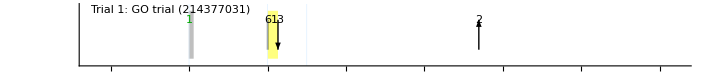

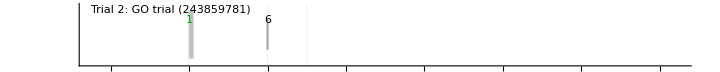

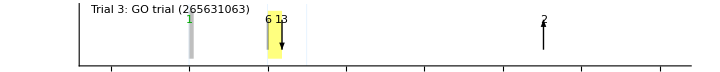

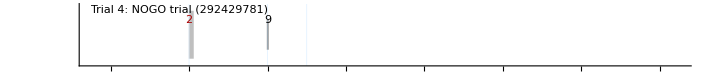

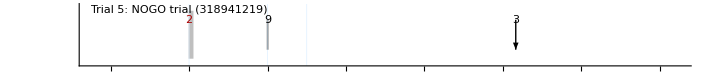

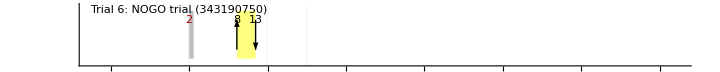

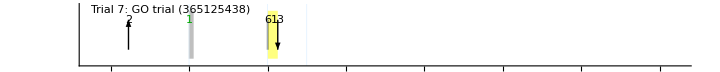

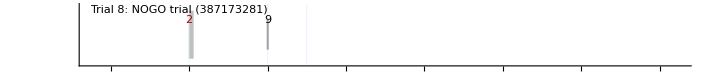

Part::partw: Part 4 of Missing["NotFound"] does not exist.

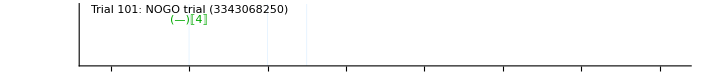

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
PPPlotTrialNumber=0;
PPPlotTrial /@ trialsColb
```

```mathematica
Length[trialsColb]
```

101

```mathematica
trialsColb[[1]]
```

{{Stimulus,214363344,249781,1,TTL Input on AcqSystem1_0 board 0 port 0 value (0x0001).,XXX},{Colbourn,214377031,0,4,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0004).,Sw1},{Colbourn,218381063,0,6,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0006).,Sw1},{Colbourn,218911188,0,13,TTL Input on AcqSystem1_0 board 0 port 1 value (0x000D).,Sw2},{Colbourn,218916406,0,1,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0001).,Sw2},{Colbourn,229150375,0,2,TTL Input on AcqSystem1_0 board 0 port 1 value (0x0002).,Sw1}}

## Import Video and Align